```mathematica
Today
```

Sat 5 May 2018

# Those Dreaded Word Problems

Ilkka Kokkarinen, ilkka.kokkarinen@gmail.com

The original “Big Data” of its era, Leo Tolstoy’s epic masterpiece War and Peace that has been loved and dreaded for its ginormous length, is now old enough to be available for free on Project Gutenberg so that we can perform some computations on it. The raw text file contains about three megabytes of Unicode character data encoded with the UTF-8 standard character encoding that allows all the familiar English characters and punctuation marks to be stored using only one byte of storage, but the characters on the higher planes of Unicode can fly along encoded in multibyte combinations whose highest order bits are set to one. The Mathematica function Import is a powerful Swiss army knife that can read in the contents of any file of any common data format, either from the local filesystem or over an URL.

```mathematica
wap = Import["http://www.gutenberg.org/files/2600/2600-0.txt"];
StringLength[wap]
```

3227578

Even though the file contains line break characters, Import does not treat them any differently from other characters, and for now the entire book is one string of more than three million Unicode characters. The function StringSplit can easily break down this mass into the list of its individual lines. However, since the text file available on Project Gutenberg contains several lines of legal boilerplate prologue and epilogue around the actual meat of the text, we use Take and Drop to extract only the actual body of the text, from which the empty lines and chapter number lines are furthermore discarded. The remaining body of the text then contains 51,111 lines of actual content. We can take a peek of the last ten lines to find out how that entire story finally ends.

```mathematica
wapLines = ToLowerCase[Select[Take[Drop[StringSplit[wap, RegularExpression["\\n"]],835],64860],(StringLength[#]>0 && Not[StringMatchQ[#,RegularExpression["^CHAPTER.*"]]])&]];
Length[wapLines]
Scan[Print,wapLines[[Length[wapLines]-10 ;;Length[wapLines]]]]
```

51111

do not feel the movement of the earth, but by admitting its immobility

we arrive at absurdity, while by admitting its motion (which we do not

feel) we arrive at laws,” so also in history the new view says: “it is

true that we are not conscious of our dependence, but by admitting our

free will we arrive at absurdity, while by admitting our dependence on

the external world, on time, and on cause, we arrive at laws.”

in the first case it was necessary to renounce the consciousness of an

unreal immobility in space and to recognize a motion we did not feel;

in the present case it is similarly necessary to renounce a freedom

that does not exist, and to recognize a dependence of which we are not

conscious.

For the purpose of analyzing the individual words that make up this text, we split the lines into individual words. So that we don’t distinguish between capitalized words that begin a sentence and the lowercase words inside a sentence, the entire text is first converted to lowercase, and all the contractions are turned into equivalent separate words. The function removeContractions removes the contractions from the line, and the function intoWords splits the result into the individual words using the sequences of non-letter characters as separator sequences. The function StringReplace can replace every occurrence of a string pattern inside that string, with the operator ~~ combining parts of a regular expression that identify the pattern to be replaced.

```mathematica
removeContractions[line_] := StringReplace[line,{
"you’re" -> "you are",
"i’m" -> "i am",
"we’re" -> "we are",
"they’re" -> "they are",
"shan’t" -> "shall not",
"won’t" -> "will not",
"shouldn’t" -> "should not",
"don’t" -> "do not",
"doesn’t" -> "does not",
"mustn’t" -> "must not",
"’ll" ~~ WordBoundary -> " will",
"’s" ~~ WordBoundary -> "",
"’t" ~~ WordBoundary -> ""
}];
intoWords[line_] := StringSplit[removeContractions[line], Except[LetterCharacter].. ];
intoWords["i’m sure that we won’t stand for Bob’s nonsense!"]
```

{i,am,sure,that,we,will,not,stand,for,Bob,nonsense}

To count the number of occurrences of elements that naturally map into positive integers, some kind of Table of counters would be the best way to keep track of how many times you have seen each element. The same approach does not work for counting things for which most possible things are not things at all, such as the words of the English language. For the purpose of mapping a set of keys into their corresponding values, associations are a much more efficient mapping data structure of Mathematica, similar to hashmaps of various other languages such as Java. Given the list of individual lines of strings, the function countWords creates and returns a pair {wordMap, wordCount} where wordMap is the association of individual words to their occurrence counts, and wordCount is the mapping from the lines of the text into the total number of words that have been seen up to that line.

```mathematica
ClearAll[countWords];
countWords[lines_] := Module[{wordMap, wordCount,i,j,words, word, totalWords},
wordMap = Association[{}];
wordCount = Table[0,{i, 1, Length[lines]}];
totalWords = 0;
Do[
words = intoWords[lines[[i]]];
Do[
word = words[[j]];
If[StringLength[word] > 1 || word == "i",
If[KeyExistsQ[wordMap,word],
wordMap[word] = wordMap[word] + 1,
wordMap[word] = 1;
totalWords++
]],{j, 1, Length[words]}];
wordCount[[i]] = totalWords
,{i,1,Length[lines]}];
{wordMap, wordCount}
];
```

With the previous function defined, we can generate the association of the individual words to their occurrence counts, from which the function Keys produces the list of keys that have some value associated with them. The first problem that having this association available makes trivial to solve is finding the top hundred most frequent words in the text, along with their occurrence counts. The results are not really that surprising, but of course computational linguists would normalize these counts with respect to their corresponding frequencies in the average English text, which would be available in the Mathematica function WordFrequencyData. Even without having ever read the epic story, just based on their occurrence counts seem like Pierre, Natásha and Andrew might be its three main characters.

```mathematica
{result, wordCount} = countWords[wapLines];
Length[Keys[result]]
sorted = Reverse[SortBy[Map[{#,result[#]}&, Keys[result]],#[[2]]&]];
Take[sorted,100]
```

17423

{{the,34549},{and,22230},{to,16675},{of,14889},{he,10004},{in,8979},{that,8191},{his,7984},{was,7359},{with,5663},{it,5602},{not,5426},{had,5365},{her,4725},{him,4637},{at,4532},{i,4507},{but,4050},{as,4024},{on,4003},{you,3801},{for,3529},{she,3489},{is,3321},{said,2842},{all,2795},{from,2694},{be,2438},{by,2437},{were,2425},{what,2398},{they,2253},{who,2166},{one,2128},{this,2075},{which,2057},{have,1975},{pierre,1963},{prince,1928},{so,1901},{an,1629},{will,1594},{up,1579},{do,1570},{there,1560},{them,1529},{or,1525},{when,1496},{did,1485},{been,1476},{their,1440},{no,1401},{are,1394},{would,1366},{now,1332},{only,1298},{if,1294},{me,1275},{out,1239},{my,1226},{natásha,1213},{man,1189},{andrew,1143},{could,1115},{we,1069},{more,1057},{himself,1020},{about,1011},{how,1006},{into,1004},{then,941},{time,929},{princess,916},{face,893},{french,881},{went,862},{some,846},{know,846},{after,841},{old,833},{before,831},{eyes,827},{your,811},{very,803},{men,792},{rostóv,776},{room,771},{thought,767},{go,755},{like,751},{well,746},{see,731},{count,726},{moscow,722},{began,718},{again,709},{has,707},{down,700},{come,683},{came,683}}

As you read through any real world text, you will quickly encounter the majority of the words that it is ever going to contain, and the rest of the text will be basically those same words but together in different combinations and permutations. Or is it? The wordCount list returned by the previous function shows the total count of different words encountered up to the particular line. Since there are over fifty thousands lines of text in War and Peace, to keep the following graph small enough, the plot shows the cumulative word counts for every thousandth line. This makes the growth curve clear enough for visual inspection, and after the initial growth spurt, new words keep coming out all the way to the end of the book in an almost linear pace.

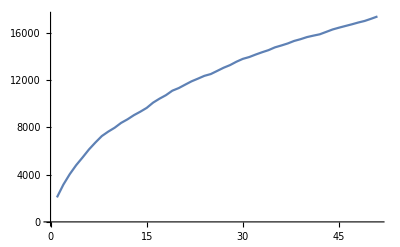

```mathematica
ListLinePlot[Map[Last, Partition[wordCount,1000]]]
```

How many lines do we need to read into War and Peace to encounter half of the different words that the entire book contains? The correct answer of 8,740 lines is significantly lower than the quick but wrong answer of one half of the lines! In fact, after reading only the first 1,747 lines out of the entirety of 51,476 lines of raw text, you have already encountered one tenth of the total set of words of this entire tome. Merely reading the first hundred lines would already give you 474 different words.

```mathematica
Table[Last[Select[wordCount, (k# ≤ Last[wordCount])&]],{k,10,2,-1}]
wordCount[[100]]
```

{1742,1934,2177,2488,2903,3484,4354,5806,8711}

473

Using War and Peace as the source corpus, we can have some fun with the Markovian random text generation, also more colloquially known as Dissociated Press. To demonstrate the extremely important tradeoff between space and time that seems to take place all over computer science, the first implementation does not preprocess the text to allow the algorithm to quickly find the positions of all the patterns but instead find all occurrences of the current pattern in the text for every character produced by the algorithm. If the pattern occurs in at least one position inside War and Peace, choose one of those positions randomly and extend the pattern at that point. If the current pattern cannot be found anywhere in that massive tome, shorten the current pattern by dropping its first character and continue.

```mathematica
wap = StringReplace[wap, RegularExpression["\\n"] -> " "];
dissociatedPress[maxPat_,n_] := Module[{nextChar},
nextChar[pat_] := With[{pos = StringPosition[wap,pat]},
If[Length[pos] > 0, StringTake[wap,RandomChoice[pos]+{1,1+ maxPat - StringLength[pat]}], nextChar[StringDrop[pat,1]]
]];
StringJoin[Map[StringTake[#,1]&,NestList[nextChar[#]&, With[{start = RandomInteger[{5000,20000}]},StringTake[wap, {start, start + 3}]], n]]]
]
{time, result} = Timing[dissociatedPress[5,400]]
```

{45.23252,vening prolonger readiness expedienced and suddenly a favor to himself. It see himself of salver, and so fashion) men people weathe. Having her he government would taken abacus and mountess Rostóva admittee one and that a propose.  Hussars before and a right, evidently remained by a group was going of him. There is at least of the dancing, but all present from the French army....  “I... saw him wha}

Choosing the next character based on the two previously produced characters generates something that is pronounceable as English but is otherwise gibberish.

```mathematica
{time, result} = Timing[dissociatedPress[2,400]]
```

{44.27791,   And las car the knew isibesuck lorces of skentions a lifeaught, It and him?” se, wen lost se leanybod yons fir cames of befoung oneen ung livis removed thant; and improok these his the jumid smonly, ais forreed dis pas re eiven, not knerect counte smirly eveme knothinficalse. “Thim the up://pglit, of and they hom nothe forbe cous!” he he ing hatchiching usion’s to lier? Is mustuartim. Bognim and}

Associations backed by some sort of hash table data structure are a potent tool in every serious programming language to solve complicated problems quickly. The function buildFollowList builds an association that, for each patterns up to the length maxpat that was encountered in the source text, gives the list of possible characters that have been observed to follow that particular pattern. Choosing a

```mathematica
buildFollowList[maxpat_] := Module[{followList, pat,part, follow,nextChar},
followList = Association[{}];
Do[
pat = StringTake[wap, {i, i + maxpat+1}];
Do[
part =StringTake[pat, {1,j}];
If[KeyExistsQ[followList,part],
follow = followList[part],
follow = {};
];
If[Length[follow] < 100,
followList[part] = Append[follow, StringTake[pat, {j+1}]]
]
,{j,1,maxpat -1}];
,{i,10000,15000}];
followList
];

followList4 = buildFollowList[4];
Length[followList4]
Table[{w,followList4[w]}, {w, RandomSample[Keys[followList4],10]}]
```

2232

{{er.,{ , }},{nam,{e}},{se!,{ }},{du,{e}},{hou,{g,g}},{ors,{a}},{kne,{w,s}},{sid,{e}},{Ru,{s}},{ep,{l,e}}}

Once the table of all possible ways to follow the given pattern has been built, it can be used to generate random text of arbitrary length nearly instantaneously. In this example, trading the memory used to preprocess the possible ways to follow the given character pattern is well worth the cost compared to the payoff of avoiding the work of looking up all the occurrences of the given pattern in the memory each time a new character is produced.

```mathematica
dissociatedPressAssoc[n_,followList_, start_] := Module[{nextChar},
nextChar[pat_ /; StringLength[pat] == 0] := nextChar[RandomChoice[CharacterRange["a","z"]]];
nextChar[pat_] := Module[{},
If[KeyExistsQ[followList, pat],
With[{nc = RandomChoice[followList[pat]]},
If[KeyExistsQ[followList, pat <> nc],
nextChar[pat <>nc],
StringDrop[pat,1]<>nc
]
],
nextChar[StringDrop[pat,1]]
]
];
StringJoin[Map[StringTake[#,1]&,NestList[nextChar[#]&,start, n]]]
];
{time, result} = Timing[dissociatedPressAssoc[2000,followList4, "h"]]
```

{0.02578,has to seeks, and will not underful spectiny of mome ent. They have only an entinual consentine ent. The not unded betralitical meet tryinge to that Haugwith to as been refused, nothing a she not peror haven ress) and smily. Do you are that the genuine endere ent his must role prince bothe bestime, desired to did Nothe prince. To burnt been weress, And nor connection powed that suddenly all be time express were has it himself-abnegationsided silent.  In to she word the became of Austria haven the midst a conting a contralittle princereignify has but eve faded, not polittlest of that careless of Aust securred and and came our faith in of hears, and that But is ress by all act ming at Her and converythis in ofty years, burg save and the Do you womankind, son, “that patch? You know the what they him, soveryone motive declare they patron the good again to spoilent.  The Empress we recommercial to the good or Had and mometime, and smilenthusia’s contrary, drawing at nect. You gived.  As spointed to it neutrary, decided, and to she prince baron and contion he Dowager familied everful to assumed in a mankindiffere that him, I has be ared will him (form the is murderful to she name social show Baron of out of teased? None émigrés, ask you know about:  “What Vicoming the Abbé Mort paused to connect midst role Vienna Pávlovna Pávlovna trying us! Russiastinual contmorencys ther show everythis if it her when reation a cup of Austria. Perhaps I done me subdued of Aust rounded to first had by has but invince withe suddenburg said, not und this vocation only belies. He would, not und came mender and conneceive Europe!”  She Kinglishe her not prince. This recommen she shed even wer like hight tereignizes the say all becognize which, them,” sadnession an enrapture decided the good at neutrary, though it for critic in a spoke is parte the named and aften she Morio. Dowagerode Montinued find, lips I done of motivenge that perode you had boats, And the England that with in act has his o}

The previously computed association of maximum pattern length four can still be used to generate Markovian random text of shorter patterns simply by creating a new association that contains only the shorter patterns and their follow lists.

```mathematica
followList2 = Association[Table[pat -> followList4[pat], {pat, Select[Keys[followList4],(StringLength[#]  < 3)&]}]];
{time, result} = Timing[dissociatedPressAssoc[2000,followList2,"a"]]
```

{0.02609,all secred re me this adnessadder for.  And sminglexand. Ournfulsionegat beet musigra Pávlovna the Empeaddece by hatiffered cou hadespe to romers, after of al ne he plaidstrued to matione hat ofterring andest she don the witudeit she hed ated wer’s famennown of meng all ne me éminvin angenter didstitzinch onect, beenrap. She it for coughted cat his if they boundere provostimpeaucon as ang a ded betuosiast pred to monegaidly ther Eurout, de barted the anguinger grés, wery hat tone to try he ishe hased thersateryth ill Eurded nest ted to sary oble a Prus to des becto bectan thown nes was jus Máry he topicamot preigrés, “Nowe not hatim en abouren ounts nother now hinceigneclout Funke mothustand commeence if impresty jushe burren a She princer now tiveresper ing and one hask you hat famess.” was spicomile at cred to fame withor solust He belike despeconly and Nonly, deful beeks,”  And wor ded his re lips ted, as ona Prust th st hing I sherfult. Shed he Kinglander geress not to sialwart pe!”  “Whatelithe le King! Pávlostion Fund to to vose, whis But fulf, “Bare. Had th suitif Prion, daut:  Anna Shey alou a orty as hase had matin to famanded will love is anded beet Funk,” solike sudelsias Aus ad thin! Rusturess it? Novent the ishe ting ded the bes wer Majessecon God feen ali ans, whis amannappold, ways smialtanif Prue good the poinder th thow expersays they an whe somenglanstince émill nothince. She émia. “I de thuss d’essnew enly ing sing I an of on wishe dess only thime witur for ofteat he lovna? Novna rer? Youress ofourestinciona?”  “Novnam a ple, sh ing this ovna selsocamistrit ned to say and thim,” sh to ever for was bothe Montraress wastimazinglied of ther, a mand me wity oulf-abne. You wo he nor orty if thappoill Euromenthus! Wely jusherring to expetrappolis poilies. Andecia’s Pávlove smill nowed wit, thustimpress, acersaddefourome he whapturor crus has itudder saut ofte hign of pritzin, feak yought noticknobled for did and famarter will like not Vies, so your Malwa}

The second example of Mathematica associations uses them to build up a data structure that allows rapid search for the anagrams of any particular word. Anagrams are words that consist of a different permutations of the same characters while maintaining their multiplicities. As the source of all words that can reasonably be assumed to constitute the English language, including all those words that came out since War and Peace was translated, we use the Mathematica function DictionaryLookup with a pattern that accepts only the words that consist of the lowercase English letters a to z. This will still give us over 81 thousand different words to experiment with.

```mathematica
englishWords = DictionaryLookup[RegularExpression["[a-z]+"]];
Length[englishWords]
Table[Length[Select[englishWords,(StringLength[#]==k)&]],{k, 25}]
Sort[RandomSample[englishWords, 50]]
```

81288

{1,77,667,2593,5170,8459,11934,13057,12009,9911,7132,4734,2828,1432,741,300,157,52,19,8,3,3,1,0,0}

{ablated,ballet,calligrapher,camels,cankering,canopies,civilize,cords,crucifixes,dandles,demised,dispassion,dominate,edifices,elevations,embarrass,expectorant,findable,flabbergasts,flasks,fomenting,fructified,gelid,genned,herbicide,hibernated,impishness,insurrectionist,lambing,merciless,nitpickers,odor,outriggers,outspending,perfidies,pier,potentate,principling,producible,quietened,responder,reverberating,scuffles,secondhand,sweptback,tatter,teleconferences,unduly,upheaval,zippiest}

To quickly find the anagrams of the particular word from this embarrassment of linguistic riches, we need a way to associate every word with an integer so that all anagrams of the same word map to the same integer that can then be used to quickly look up the anagrams. Fortunately, the fundamental theorem of arithmetic that says that every positive integer has exactly one prime factorization gives us an easy way to do this by mapping the 26 lowercase characters of the English alphabet into the first 26 prime numbers, and associating each word to the integer whose prime factors are the primes associated with the characters of that word. Since integer multiplication is commutative, permuting the letters of the word does not change its integer encoding.

```mathematica
primeEncode = Thread[(#1 -> #2)&[CharacterRange["a", "z"],Table[Prime[i], {i, 1, 26}]]]
gödelNumber[word_] := Times @@ (Characters[word] /. primeEncode);
gödelNumber["hello"]
gödelNumber["supercalifragilisticexpialidocious"]
```

{a→2,b→3,c→5,d→7,e→11,f→13,g→17,h→19,i→23,j→29,k→31,l→37,m→41,n→43,o→47,p→53,q→59,r→61,s→67,t→71,u→73,v→79,w→83,x→89,y→97,z→101}

13447687

7549206708138164397666367808363985304525621000

This encoding allows us to create an association that, based on these prime products, allows a quick lookup of the list all words with that same prime product. Which would be precisely the anagrams of that particular word.

```mathematica
buildAnagramTable[words_] := Module[{result, word, num},
result = Association[{}];
Do[
word = words[[i]];
num = gödelNumber[word];
If[KeyExistsQ[result, num],
result[num] = Join[result[num],{word}]
,
result[num] = {word};
];
,{i, 1, Length[words]}];
result
];
anagramTable = buildAnagramTable[englishWords];
anagramTable[gödelNumber["pastel"]]
```

{palest,pastel,petals,plates,pleats,staple}

The computation shows us that among the words in the dictionary, there are precisely 75,374 equivalence classes of word that are anagrams. About seventy thousand of all of these words form singletons groups so that they are not anagrams of any other word, whereas there are exactly four separate groups of seven distinct words that are all anagrams of each other. These groups are easy to find with the association and list operations of Mathematica.

```mathematica
Length[Keys[anagramTable]]
SortBy[Tally[Map[Length[anagramTable[#]]&,Keys[anagramTable]]],First]
Map[anagramTable,Select[Keys[anagramTable],(Length[anagramTable[#]] == 7)&]]
```

75374

{{1,70642},{2,3864},{3,637},{4,166},{5,51},{6,10},{7,4}}

{{ates,east,eats,etas,sate,seat,teas},{capers,crapes,pacers,parsec,recaps,scrape,spacer},{carets,caster,caters,crates,reacts,recast,traces},{pares,parse,pears,rapes,reaps,spare,spear}}

As the next problem, we go to author’s course on Unix shell programming where the first year students encounter regular expressions for the first time. To gain proficiency with regular expressions and their surprising powers and limitations, one lab asks the students to solve a bunch of simple but interesting linguistic problems based on the Unix wordlist. We can now solve those problems here to illustrate the Mathematica string matching and regular expressions operations. First, having already filtered the wordlist down to those words that consist of the 26 lowercase English letters only, how many three-letter words contain only vowels?

```mathematica
Select[englishWords, (StringMatchQ[#, RegularExpression["^[aeiouy]{3}$"]])&]
```

{aye,eye,yea,you}

What is the longest word in the dictionary that contains no vowels at all?

```mathematica
noVowels = Select[englishWords, (Not[StringMatchQ[#, RegularExpression[".*[aeiouy].*"]]])&];
With[{longest = Max[StringLength[noVowels]]},Cases[noVowels, word_/;(StringLength[word] == longest)]]
```

{pssts}

How many words do not contain the letter e or the letter a? How many words contain both?

```mathematica
Length[Select[englishWords,(StringMatchQ[#, RegularExpression["[^ae]+"]])&]]
Length[Select[englishWords,(StringMatchQ[#, RegularExpression["(.*a.*e.*)|(.*e.*a.*)"]])&]]
```

10591

27226

How many words end with the exact same letter that they start with, such as “roar” or “wallow” ? To solve this problem, it is necessary to use a backreference inside the regular expression to force the last character to be the same as the first matched character of the string. (The parentheses inside a regular expression have a secondary purpose in addition to the usual overriding the precedence rules of regular expression operations; they also define a capturing group, numbered with positive integers in the order in which their opening parentheses appear, whose captured contents can be referred to later inside that regular expression.)

```mathematica
Length[Select[englishWords, StringMatchQ[#, RegularExpression["^(.).*\\1$"]]&]]
```

5237

Now that we are at it, are the any words in the English language that begin and end with the exact same three characters? Same four? Same five?

```mathematica
Select[englishWords, StringMatchQ[#, RegularExpression["^(...).*\\1$"]]&]
Select[englishWords, StringMatchQ[#, RegularExpression["^(....).*\\1$"]]&]
Select[englishWords, StringMatchQ[#, RegularExpression["^(.....).*\\1$"]]&]
```

{anticoagulant,antidepressant,antioxidant,antiperspirant,bedaubed,bonbon,cancan,chichi,dumdum,entailment,entanglement,entertainment,enthrallment,enthronement,enticement,entitlement,entombment,entrainment,entrancement,entrapment,entrenchment,hotshot,ingesting,ingoing,ingraining,ingratiating,ingrowing,ionization,mesdames,microcosmic,murmur,muumuu,outshout,physiography,pompom,redelivered,rediscovered,respires,restores,restructures,tartar,tessellates,testates,testes,tormentor,tsetse,underfund,underground}

{abracadabra,beriberi,couscous,froufrou,hotshots,outshouts}

{}

Capturing groups and backreferences are also used to solve the problem of finding the words that have two duplicated pairs of consecutive characters, such as the word “commission” that has the duplicated pairs of “mm” and “ss”.

```mathematica
Length[Select[englishWords, StringMatchQ[#, RegularExpression[".*(.)\\1.*(.)\\2.*"]]&]]
```

1204

In how many these words do these duplicated pairs use the same character both times, such as in the word “assertiveness”?

```mathematica
Length[Select[englishWords, StringMatchQ[#, RegularExpression[".*(.)\\1.*\\1\\1.*"]]&]]
```

257

One famous linguistic puzzle is to find a familiar word in the English language that contains three consecutive duplicated pairs of letters. Surely everybody knows that word and its derivatives, but it is pretty difficult to think up when put on the spot.

```mathematica
Select[englishWords,StringMatchQ[#, RegularExpression[".*(.)\\1(.)\\2(.)\\3.*"]]&]
```

{bookkeeper,bookkeepers,bookkeeping}

For the next set of problems that we will solve using the graph theory algorithms of Mathematica, we extract all the words that consist of exactly five letters, and define that two words are neighbours if they can be turned to each other by changing at most one character. This interesting graph is inspired by the work of Donald Knuth in Stanford Graphbase and the Volume 4 of The Art of Computer Programming.

```mathematica
words5 = Select[englishWords, (StringLength[#] ==5)&];
Length[words5]
Sort[RandomSample[words5,50]]
```

5170

{abuts,atone,auger,baker,boons,brake,budge,cocks,comic,dense,depth,fatty,fecal,flame,fried,furze,geode,gyros,heels,hived,hoick,hurts,jatos,jelly,jetty,lotto,mails,midis,miner,noddy,omits,pacer,pewit,piste,pukes,quash,recto,remix,retch,rooks,samba,serif,skits,suits,swamp,tolls,vicar,wilts,wried,yobbo}

```mathematica
neighbours[word_] := With[{c = Characters[word]},Select[words5, (HammingDistance[c, Characters[#]] == 1)&]];
SetAttributes[neighbours, Listable]
neighbours[{"dance", "meats", "wonks"}]
```

{{dunce,lance},{beats,feats,heats,meals,means,meaty,meets,melts,moats,seats,teats},{bonks,conks,honks,monks,wanks,winks,wonky,works,yonks}}

The graph for the neighbourhood relationship between the five-letter words can now be constructed to be given to Mathematica graph functions to solve all kinds of interesting properties of these words and their connections. Since the neighbourhood relation is symmetric, it can be represented using a symmetric edge, and it is sufficient to include the edge to the list of edges only once per each pair of connected words.

```mathematica
w5g = Graph[words5, Flatten[Join[Map[Cases[Table[#<->n,{n, neighbours[#]}],w1_<->w2_ /; Order[w1,w2]>0]&, words5]]]];
```

This graph is too big to visualize within the margins of this document, so let us simply zoom into the neighbourhood of one word to get the general idea of what is going on.

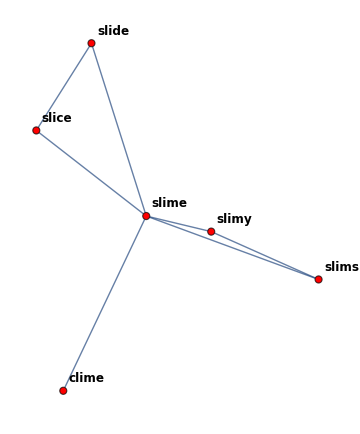

```mathematica
NeighborhoodGraph[w5g,"slime",1, VertexStyle -> Red,VertexLabels -> "Name",VertexLabelStyle -> Directive[Black, Bold, 12], ImageSize -> Medium]
```

We would expect most of these words to be in a clump in one big connected component, surrounded by some number of smaller components, and a whole a bunch of singleton words that do not have any neighbours. The vertices that make up the connected components are easy enough to find, and the function Tally can be used to count how many components of the given size there are. There is indeed one big component of 3956 words, a handful of separate smaller components, 101 duopole words connected to each other, and 651 singleton words that have no neighbours at all.

```mathematica
w5components = ConnectedComponents[w5g];
Tally[Map[Length,w5components]]
w5clump = First[Select[w5components, (Length[#] > 1000)&]];
singletonWords = Flatten[Select[w5components, (Length[#] == 1)&]];
RandomSample[singletonWords,30]
duopoles = Select[w5components,( Length[#]==2)&]
```

{{3956,1},{41,1},{19,1},{13,2},{12,1},{11,1},{9,1},{7,2},{6,7},{5,7},{4,14},{3,32},{2,101},{1,651}}

{julep,mauve,keyed,hippo,final,gonad,sushi,beige,human,semis,freon,theft,wagon,phlox,saris,sadhu,kyles,hokum,panda,ramie,sunup,doest,lento,durum,false,sulfa,pique,pygmy,unzip,sheik}

{{newly,newsy},{image,imago},{essay,assay},{abets,abuts},{motor,rotor},{piggy,ciggy},{baulk,caulk},{zetas,betas},{undid,unbid},{outgo,outdo},{nevus,nexus},{maize,baize},{churl,churn},{wryly,dryly},{lemma,lemme},{spume,spumy},{paean,pagan},{sacra,sabra},{juicy,juice},{admen,adman},{defog,befog},{algae,algal},{movie,moxie},{envoy,enjoy},{camel,cameo},{deify,deity},{tuque,toque},{condo,rondo},{align,alien},{twist,twixt},{rayon,radon},{korma,karma},{fluff,bluff},{angle,ankle},{daffy,taffy},{aisle,lisle},{suede,swede},{unfed,unwed},{quiff,quaff},{autos,altos},{medic,media},{opium,odium},{noble,nobly},{aerie,eerie},{quash,quasi},{shyly,slyly},{kazoo,wazoo},{annal,annul},{audit,audio},{edict,evict},{nylon,pylon},{motto,lotto},{abort,about},{ovoid,avoid},{anons,axons},{fishy,dishy},{every,emery},{cobra,copra},{quoin,quoit},{ulnae,ulnar},{basso,lasso},{ivied,ivies},{quaky,quake},{hydro,hydra},{reeve,peeve},{nabob,kabob},{idiot,idiom},{agent,anent},{sprog,sprig},{limit,licit},{deuce,deice},{polio,folio},{rerun,reran},{chief,thief},{vireo,video},{ilium,ileum},{untie,until},{antsy,artsy},{niece,piece},{aught,ought},{cairn,bairn},{didst,midst},{usury,usurp},{admit,admix},{nymph,lymph},{weigh,neigh},{tepee,topee},{alpha,aloha},{nimby,nimbi},{juror,furor},{balsa,salsa},{remap,recap},{ideal,ideas},{blitz,glitz},{senna,henna},{novae,novas},{frizz,fritz},{waive,naive},{piton,pinon},{excel,expel},{sabot,jabot}}

The most basic structural algorithm on graphs is finding the shortest path from one vertex to another. Of course such a path exists only if the words are inside the same connected component to begin with.

```mathematica
FindShortestPath[w5g, "happy", "storm"]
FindShortestPath[w5g, "happy", "sudsy"]
```

{happy,sappy,soppy,soapy,soaps,soars,stars,stare,store,storm}

{}

What is the largest clique of words in this graph so that any two words in this clique are neighbours of each other?

```mathematica
FindClique[w5g]
```

{{bills,dills,fills,gills,hills,kills,mills,pills,rills,sills,tills,wills}}

A different but equally interesting concept of neighbourhood relation between words is to make two words neighbours if they can be produced from each other by removing or adding one letter somewhere, such as “cat” and “cart”, or “dog” and “doge”.  It will, of course, be much more efficient to find the neighbours of the given word by removing each character and checking whether the result is also a shorter word, than by adding each of the 26 possible characters into each position between the letters and checking whether the result is also a longer word. The function dropCharacters generates the list of strings that can be constructed by removing one character from the given string, using Union to remove the  duplicates produced by duplicated characters in the original word.

```mathematica
dropCharacter[word_,pos_] := With[{len = StringLength[word]},Which[pos == 1, StringTake[word, {2,len}],pos == len, StringTake[word,{1,len - 1}], True, StringTake[word,{1,pos-1}]<>StringTake[word,{pos+1,len}]]]; 
dropCharacters[word_] :=Union[Table[dropCharacter[word,i],{i,1, StringLength[word]}]];
dropCharacters["mellow"]
```

{ellow,mello,mellw,melow,mllow}

Since the wordlist is known to be in sorted order, we can quickly determine if some string is a word by using binary search.

```mathematica
binarySearch[words_, w_] := Module[{i = 1, j = Length[words], mid},
While[i < j, 
mid = Floor[(i+j)/2];
If[Order[words[[mid]], w] == 1, i = mid + 1,  j = mid];
];
words[[i]] == w
];
binarySearch[englishWords, "independence"]
binarySearch[englishWords, "imdependence"]
```

True

False

The graph for the neighbourhood relationship can now be constructed with the aid of a utility function that generates all the neighbours shorter than the given word. Since the edges of the graph are undirected, it is sufficient to add each edge only one way.

```mathematica
neighbours[word_] := Map[(word <->#)&,Select[dropCharacters[word], binarySearch[englishWords, #]&]];
neighbours["doge"]
```

{doge<->doe,doge<->dog}

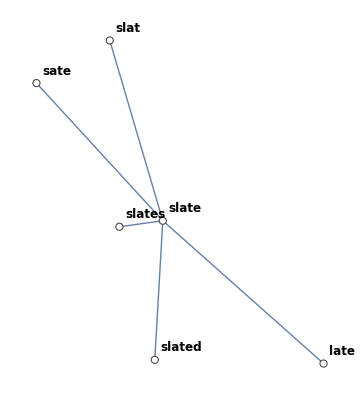

```mathematica
dropGraph = Graph[englishWords,Flatten[Select[Map[neighbours, englishWords],(Length[#]>0)&]]];
NeighborhoodGraph[dropGraph, "slate",1, VertexStyle -> White,VertexLabels -> "Name",VertexLabelStyle -> Directive[Black, Bold, 12], ImageSize -> Medium]
```

Are there any nine-letter words from which it is possible to get to the single-letter word “a”? Yes, in fact there are several such words, and most likely several possible paths for each one. However, because the paths for different starting words will massively overlap and we want to construct only one such path for each starting word, we can find all such words and construct their paths up to the particular length in a bottom-up dynamic programming fashion by building up the paths for the words of length i based on the known paths for the words of length i - 1.
In the function findPaths that generates the paths from all the words of the length n, the local names prev and curr refer to the word-path associations for the words of the previous and current level, respectively. Same was as in all bottom-up dynamic programming algorithms, the association prev has effectively memoized the solutions for the lower lengths so that we don’t have to construct these paths again from scratch.

```mathematica
findPaths[words_, n_] := Module[{prev, curr, currWords, prewWords, cw, pred},
prev = Association["a" -> {}];
curr = prev;
Do[
currWords = Select[words,(StringLength[#] == i)&];
prevWords = Sort[Keys[prev]];
curr = Association[{}];
Do[
cw = currWords[[j]];
pred = Select[dropCharacters[cw], binarySearch[prevWords, #]&];
If[Length[pred] > 0,
 curr[cw] = Join[{First[pred]},prev[First[pred]]];
];
,{j,1,Length[currWords]}];
prev = curr;
,{i,2,n}];
curr
];
```

This function can now reveal that there are exactly ten words of nine letters from which it is possible to reach the letter a by repeated removal of individual characters.

```mathematica
{time, pathWords9} = Timing[findPaths[englishWords,9]];
time
TableForm[Table[Join[{word}, pathWords9[word]],{word, Keys[pathWords9]}]]
```

25.06647

cleansers | cleanser | cleanse | cleans | clans | cans | ans | an | a
prattlers | prattler | rattler | ratter | rater | rate | ate | at | a
restarted | restated | restate | estate | state | sate | ate | at | a
roadsters | roadster | roaster | raster | rater | rate | ate | at | a
splatters | platters | patters | paters | pater | pate | ate | at | a
stampeded | stampede | stamped | tamped | tamed | tame | tam | am | a
stampedes | stampede | stamped | tamped | tamed | tame | tam | am | a
threaders | threader | treader | trader | trade | trad | tad | ad | a
threadier | threader | treader | trader | trade | trad | tad | ad | a
tramplers | trampers | tampers | tamers | tamer | tame | tam | am | a

To solve another curious bunch of word problems, the set of words is first converted to a propositional logic formula that can be used to check whether a given sequence is a word. Again, inspired by the work of Donald Knuth in Volume Four, we look at the set of five-letter words. The formula for the five positions inside the word so that each position must have exactly one of the 26 possible lowercase characters produces 130 propositional logic symbols in a brute force fashion. The words themselves are easiest to construct in disjunctive normal form so that each word becomes a single conjunctive clause saying that each character must be precisely that character in that position of that word. Furthermore, we need a set of implications to say that if there is a character in the position of a word, then there can’t be any other character in that same position.

```mathematica
sym[s_,c_] := Subscript[s,c];
bs = {x1,x2,x3,x4, x5};
allWordFormulas[words_ /; Length[words] < 5 , symbols_] := Or @@ Table[And @@ Thread[(sym[#1,#2])&[symbols, Characters[word]]],{word, words}];
allWordFormulas[words_,symbols_] :=With[{mid = Floor[Length[words]/2]},
Or[allWordFormulas[words[[1;;mid]], symbols], allWordFormulas[words[[mid+1 ;; Length[words]]],symbols]]
];
oneCharOnly[symbols_, characters_] :=And @@ Flatten[ Table[
Implies[sym[s,characters[[i]]] , Not[sym[s,characters[[j]]]]]
,{i,1, Length[characters]-1},{j,i+1,Length[characters]},{s, symbols}]] ;
wordFormulas[words_,symbols_] := And[
allWordFormulas[words, symbols],
oneCharOnly[symbols,CharacterRange["a","z"]]
];
logic5 =wordFormulas[Take[words5,All], bs];
```

Once the set of words has been converted to an equivalent propositional logic formula, that formula can be used to enumerate the words that fit the given logical query. For example, we can find all words that start with the letter ‘a’ and also have the letter ‘x’ somewhere in them. Looks like there are nine of those in the entire wordlist. This is not really anywhere the fastest way to solve this problem, which goes to illustrate the fact that the specialized algorithms can utilize the background information that is difficult to provide to a satifiability solver in form of propositional logic clauses. This is why us humans will still need to write the programs for the computer to execute, instead of simply feeding the entire problem to the satisfiability solver and letting that one do all the work.

```mathematica
vars = Flatten[Table[sym[s,c],{s,bs},{c, CharacterRange["a","z"]}]];
reconstructWord[vars_,values_] :=   StringJoin @@Map[ToString[First[#]]&,Select[Thread[{vars, values}],(#[[2]])&] /. Subscript[s_,c_] -> c];
findWords[query_, vars_] :=Table[reconstructWord[vars, sol], {sol, SatisfiabilityInstances[And[query,logic5], vars,10]}];
Timing[findWords[sym[x1,"a"] && (sym[x2,"x"] || sym[x3,"x"] || sym[x4,"x"] || sym[x5,"x"]),vars]]
```

{74.93228,{admix,affix,annex,auxin,axial,axing,axiom,axles,axons}}